```mathematica
Mu=0.62;
γ=5/3;
ν=0;

kRoss=21.1; (* Rosseland opacity at 0.7 Rsun*)
χ=10^3*(16*T[Rper,zper]^3*sigmaSB*(γ-1)*Mu*mP)/(3*kRoss*ρ[Rper,zper]^2*kB)   (*this is what Goldreich and Schubert call χ*)
ξradiative = (γ-1)*χ   (*this is what Balbus and Schaan call ξrad*)
```

2.13929×10^10

1.42619×10^10

```mathematica
kR[t_]:=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]:=kϕ0;
kz[t_]:=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];
k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);
```

```mathematica
DispersionRelationGS:=q^3+q^2*((2*ν*k[t]^2)/Ω[Rper,zper]+(χ*k[t]^2)/(γ*Ω[Rper,zper]))+q*((kz[t]/k[t])^2*1/(γ*Ω[Rper,zper]^2 ρ[Rper,zper])*(PdR[Rper,zper]-kR[t]/kz[t] Pdz[Rper,zper])(kR[t]/kz[t] σdz[Rper,zper]-σdR[Rper,zper])+2/(Ω[Rper,zper]*Rper)(kz[t]/k[t])^2(ldR-kR[t]/kz[t] ldz)+2/γ*((χ*k[t]^2)/Ω[Rper,zper])((ν*k[t]^2)/Ω[Rper,zper])+((ν*k[t]^2)/Ω[Rper,zper])^2)+((kz[t]/k[t])^2*1/(γ*Ω[Rper,zper]^2 ρ[Rper,zper])*((ν*k[t]^2)/Ω[Rper,zper])(PdR[Rper,zper]-kR[t]/kz[t] Pdz[Rper,zper])(kR[t]/kz[t] σdz[Rper,zper]-σdR[Rper,zper])+2/(γ*Ω[Rper,zper]*Rper)(kz[t]/k[t])^2((χ*k[t]^2)/Ω[Rper,zper])(ldR-kR[t]/kz[t] ldz)+1/γ((χ*k[t]^2)/Ω[Rper,zper])((ν*k[t]^2)/Ω[Rper,zper])^2)==0
```

```mathematica
LastTermGS[kR_,kz_]:=(kz^2/(kR^2+kz^2))*1/(γ*Ω[Rper,zper]^2 ρ[Rper,zper])*((ν*(kR^2+kz^2))/Ω[Rper,zper])(PdR[Rper,zper]+ρ[Rper,zper]*Ω[Rper,zper]^2*Rper-kR/kz Pdz[Rper,zper])(kR/kz σdz[Rper,zper]-σdR[Rper,zper])+(2/(γ*Ω[Rper,zper]*Rper))(kz^2/(kR^2+kz^2))((χ*(kR^2+kz^2))/Ω[Rper,zper])(ldR-kR/kz ldz)+1/γ((χ*(kR^2+kz^2))/Ω[Rper,zper])((ν*(kR^2+kz^2))/Ω[Rper,zper])^2
```

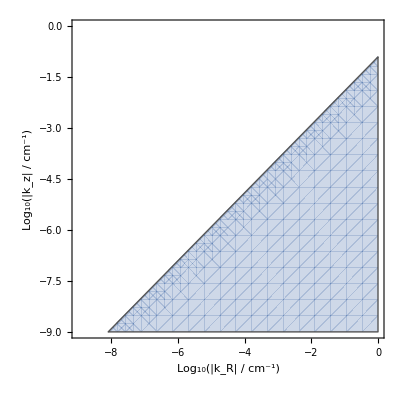

```mathematica
rper=0.7Rsun;
θper=45*Pi/180;

Rper:=rper*Sin[θper];
zper:=rper*Cos[θper];
R1at45=RegionPlot[LastTermGS[10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R > 0, k_z > 0, ν = 0"},LabelStyle->Black,BaseStyle->{FontWeight->"Bold",FontSize->12}];
R2at45=RegionPlot[LastTermGS[-10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R < 0, k_z > 0, ν = 0"},LabelStyle->Black,BoundaryStyle->{Darker[Gray],Thick},BaseStyle->{FontWeight->"Bold",FontSize->12}]
R3at45=RegionPlot[LastTermGS[10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R > 0, k_z < 0, ν = 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
R4at45=RegionPlot[LastTermGS[-10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R < 0, k_z < 0, ν = 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
```

```mathematica
rper=0.7Rsun;
θper=20*Pi/180;

Rper:=rper*Sin[θper];
zper:=rper*Cos[θper];

R1at20=RegionPlot[LastTermGS[10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R > 0, k_z > 0, ν = 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
R2at20=RegionPlot[LastTermGS[-10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R < 0, k_z > 0, ν = 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
R3at20=RegionPlot[LastTermGS[10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R > 0, k_z < 0, ν = 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
R4at20=RegionPlot[LastTermGS[-10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R < 0, k_z < 0, ν = 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
```

```mathematica
rper=0.7Rsun;
θper=70*Pi/180;

Rper:=rper*Sin[θper];
zper:=rper*Cos[θper];

R1at70=RegionPlot[LastTermGS[10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R > 0, k_z > 0, ν = 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
R2at70=RegionPlot[LastTermGS[-10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R < 0, k_z > 0, ν = 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
R3at70=RegionPlot[LastTermGS[10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R > 0, k_z < 0, ν = 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
R4at70=RegionPlot[LastTermGS[-10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R < 0, k_z < 0, ν = 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
```

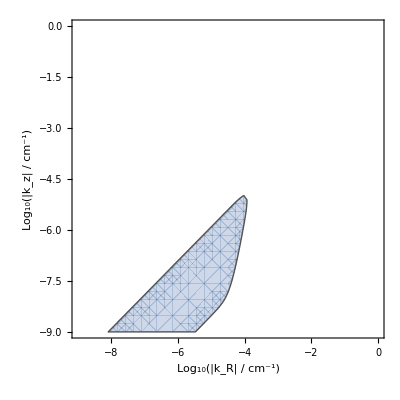

```mathematica
ν=23;

rper=0.7Rsun;
θper=45*Pi/180;

Rper:=rper*Sin[θper];
zper:=rper*Cos[θper];
R1at45withν=RegionPlot[LastTermGS[10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R > 0, k_z > 0, ν = 23 cm^2 s^-1"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
R2at45withν=RegionPlot[LastTermGS[-10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R < 0, k_z > 0, ξ_rad = 10^3 ξ_(rad⊙), ν = ν_⊙"},LabelStyle->Black,BoundaryStyle->{Darker[Gray],Thick},BaseStyle->{FontWeight->"Bold",FontSize->12}]
R3at45withν=RegionPlot[LastTermGS[10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R > 0, k_z < 0, ν = 23 cm^2 s^-1"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
R4at45withν=RegionPlot[LastTermGS[-10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R < 0, k_z < 0, ν = 23 cm^2 s^-1"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
```

```mathematica
ν=23;

rper=0.7Rsun;
θper=20*Pi/180;

Rper:=rper*Sin[θper];
zper:=rper*Cos[θper];
R1at20withν=RegionPlot[LastTermGS[10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R > 0, k_z > 0, ν = 23 cm^2 s^-1"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
R2at20withν=RegionPlot[LastTermGS[-10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R < 0, k_z > 0, ν = 23 cm^2 s^-1"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
R3at20withν=RegionPlot[LastTermGS[10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R > 0, k_z < 0, ν = 23 cm^2 s^-1"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
R4at20withν=RegionPlot[LastTermGS[-10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R < 0, k_z < 0, ν = 23 cm^2 s^-1"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
```

```mathematica
ν=23;

rper=0.7Rsun;
θper=70*Pi/180;

Rper:=rper*Sin[θper];
zper:=rper*Cos[θper];
R1at70withν=RegionPlot[LastTermGS[10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R > 0, k_z > 0, ν = 23 cm^2 s^-1"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
R2at70withν=RegionPlot[LastTermGS[-10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R < 0, k_z > 0, ν = 23 cm^2 s^-1"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
R3at70withν=RegionPlot[LastTermGS[10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R > 0, k_z < 0, ν = 23 cm^2 s^-1"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
R4at70withν=RegionPlot[LastTermGS[-10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-9,0},{LogKappaz,-9,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R < 0, k_z < 0, ν = 23 cm^2 s^-1"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
```

```mathematica
ν=23;
rper=0.7Rsun;
θper=45*Pi/180;

FullTgrowthkRkzTable=Flatten[Table[kR0:=-10^i;
kϕ0:=0;
kz0:=10^j;
{i,j,Log10[1/(Ω[Rper,zper]*q/.NSolve[DispersionRelationGS/.{t->0},q][[3]])]},{i,-8,-3.5,0.05},{j,-9,-4.5,0.05}],1];
TgrowthkRkzTable=Select[FullTgrowthkRkzTable,Re[#[[3]]]>0&];
```

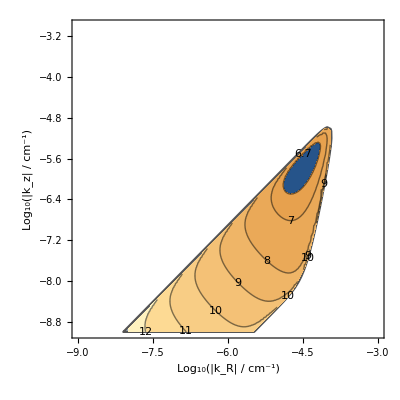

```mathematica
TGrowthPlotat45withνTemp=ListContourPlot[TgrowthkRkzTable,PlotRange->{{-9,-3},{-9,-3}},PlotLegends->BarLegend[Automatic,LegendMarkerSize->200,LegendFunction->"Frame",LegendMargins->4,LegendLabel->"Log_10(T_gr/s)",LabelStyle->{FontSize->12}],FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R < 0, k_z > 0, ξ_rad = 10^3 ξ_(rad⊙), ν = ν_⊙"},LabelStyle->Black,Contours->{6.7,7,8,9,10,11,12},ContourLabels->All,ContourStyle->Thick,BaseStyle->{FontWeight->"Bold",FontSize->12}];
R2at45withνSmaller=RegionPlot[LastTermGS[-10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-9,-3},{LogKappaz,-9,-3},FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R < 0, k_z > 0, ξ_rad = 10^3 ξ_(rad⊙), ν = ν_⊙"},LabelStyle->Black,BoundaryStyle->{Darker[Gray],Thick},BaseStyle->{FontWeight->"Bold",FontSize->12}];
TGrowthPlotat45withν=Show[R2at45withνSmaller,TGrowthPlotat45withνTemp]
```

```mathematica
ν=0;
Select[Flatten[Table[k0=10^i;
rper=0.7Rsun;
θper=θperdeg*Pi/180;
Rper:=rper*Sin[θper];
zper:=rper*Cos[θper];
kRinf=k0*dLogΩdLogR;
kzinf=k0*dLogΩdLogz;
{k0,θper,LastTermGS[kRinf,kzinf]},{i,-9,-1,0.5},{θperdeg,10,80,5}],1],Re[#[[3]]]<0&]

ν=23;
Select[Flatten[Table[k0=10^i;
rper=0.7Rsun;
θper=θperdeg*Pi/180;
Rper:=rper*Sin[θper];
zper:=rper*Cos[θper];
kRinf=k0*dLogΩdLogR;
kzinf=k0*dLogΩdLogz;
{k0,θper,LastTermGS[kRinf,kzinf]},{i,-9,-1,0.5},{θperdeg,10,80,5}],1],Re[#[[3]]]<0&]
```

{}

{}

```mathematica
rper=0.7Rsun;
θper=45*Pi/180;
Rper:=rper*Sin[θper];
zper:=rper*Cos[θper];
10^-4/(Ω[Rper,zper]*dLogΩdLogR)
```

-346.865

```mathematica
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\GoldreichSchubert - Revisited\\GS - Model A - Higher Thermal Diffusion\\picGS1.png",R2at45,ImageResolution->150];
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\GoldreichSchubert - Revisited\\GS - Model A - Higher Thermal Diffusion\\picGS2.png",R2at45withν,ImageResolution->150];
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\GoldreichSchubert - Revisited\\GS - Model A - Higher Thermal Diffusion\\picGS3.png",TGrowthPlotat45withν,ImageResolution->150];
```